## Ham for 2-band quadratic disp mode;

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={kx-> k Sin[θ] Cos[ϕ],ky-> k Sin[θ] Sin[ϕ],kp-> k Sin[θ],kz-> k Cos[θ],χ^2->1};
ass=Assumptions->{χ,vz,v,k,kp,θ,ϕ,θp,ϕp,kx,ky,kz,ek}∈ Reals &&  k>0 && kp>0 && ek>0 && v>0 && vz>0;
```

```mathematica
(*-Graphics- from PRB 110, L121122 (2024)*)
```

```mathematica
sx=PauliMatrix[1];sy=PauliMatrix[2];sz=PauliMatrix[3];s0=IdentityMatrix[2];
Clear[ham,eval,χ];v=vf;vz=vf;
{dx,dy,dz}={2χ v vz kz ky,2χ v vz kz kx,v^2(kx^2+ky^2)-vz^2 kz^2};
ham=dx sx+dy sy+dz sz;
ham//MatrixForm
{en, vec}=FullSimplify[Eigensystem[ham]/.χ^2->1,ass];
vec
FullSimplify[{en,vec}/.rep,ass]
```

((kx^2+ky^2) vf^2-kz^2 vf^2 | -2 ⅈ kx kz vf^2 χ+2 ky kz vf^2 χ
2 ⅈ kx kz vf^2 χ+2 ky kz vf^2 χ | -((kx^2+ky^2) vf^2)+kz^2 vf^2)

{{(ⅈ kz)/(kx χ-ⅈ ky χ),1},{(-ⅈ kx+ky)/(kz χ),1}}

{{-k^2 vf^2,k^2 vf^2},{{(ⅈ ⅇ^(ⅈ ϕ) Cot[θ])/χ,1},{((-ⅈ Cos[ϕ]+Sin[ϕ]) Tan[θ])/χ,1}}}

```mathematica
-ⅈ ⅇ^(ⅈ ϕ)==-ⅈ Cos[ϕ]+Sin[ϕ]//FullSimplify
```

True

```mathematica
Cos[θ]{χ(-ⅈ Cos[ϕ]+Sin[ϕ]) Tan[θ],1}/.{-ⅈ Cos[ϕ]+Sin[ϕ]->-ⅈ ⅇ^(ⅈ ϕ)}
```

{-ⅈ ⅇ^(ⅈ ϕ) χ Sin[θ],Cos[θ]}

## matrices

```mathematica
Clear[vec1,vec1dag];
vec1[θ_,ϕ_,χ_]={-ⅈ ⅇ^(ⅈ ϕ) χ Sin[θ],Cos[θ]};
vec1dag[θ_,ϕ_,χ_]={ⅈ ⅇ^(-ⅈ ϕ) χ Sin[θ],Cos[θ]};
FullSimplify[vec1dag[θ,ϕ,1].vec1[θ,ϕ,1]/.rep,ass]
(*********)
vec2[θ_,ϕ_,χ_]={χ ⅈ ⅇ^(ⅈ ϕ) Cot[θ],1};
vec2dag[θ_,ϕ_,χ_]={-χ ⅈ ⅇ^(-ⅈ ϕ) Cot[θ],1};
FullSimplify[vec1dag[θ,ϕ,1].vec1[θ,ϕ,1]/.rep,ass]
```

1

1

```mathematica
int=((vec1dag[θ,ϕ,χ].vec1[θp,ϕp,χp])(vec1dag[θp,ϕp,χp].vec1[θ,ϕ,χ]))/(2π)
amp=FullSimplify[Integrate[int,{ϕp,0,2π},ass]/. {χ^2->1,χp^2->1},ass]
```

((Cos[θ] Cos[θp]+ⅇ^(ⅈ ϕ-ⅈ ϕp) χ χp Sin[θ] Sin[θp]) (Cos[θ] Cos[θp]+ⅇ^(-ⅈ ϕ+ⅈ ϕp) χ χp Sin[θ] Sin[θp]))/(2 π)

1/2 (1+Cos[2 θ] Cos[2 θp])

```mathematica
Clear[eq,c2t,c2tp,Λ1byτ,Λ2byτ,lhs1,lhs2,rhs1,rhs2,λ1,a1,h1,λ2,a2,h2,eqn1,eqn2,eqn3,eqn4];
G=1+c2t c2tp;
Λ1byτ=-h1+λ1+a1 c2t(* Cos[2θ] *);
Λ2byτ=-h2+λ2+a2 c2t;

lhs1=λ1+a1 c2t;
lhs2=λ2+a2 c2t;    
rhs1=1/2 βintra intθpf1(-h1+λ1+a1 c2tp)G+1/2 βinter intθpf2(-h2+λ2+a2 c2tp)G;
rhs2=1/2 βintra intθpf2(-h2+λ2+a2 c2tp)G+1/2 βinter intθpf1(-h1+λ1+a1 c2tp)G;

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{c2t,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{c2t,0,1}]//FullSimplify;
eq==eqn1+eqn2 c2t//FullSimplify

eq=lhs2-rhs2;
eqn3=SeriesCoefficient[eq,{c2t,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{c2t,0,1}]//FullSimplify;
eq==eqn3+eqn4 c2t//FullSimplify
```

True

True

```mathematica
Clear[arr,array,cmat1,cmat2];arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{λ1,a1,λ2,a2}];
array=(Normal[arr]//FullSimplify)/.c2tp->c2t;
cmat1=array[[1]]//Expand;cmat2=array[[2]];
rep1={c2t h1 intθpf1->hc2t,c2t h2 intθpf2->hc2t,h1 intθpf1->hzero,h2 intθpf2->hzero,c2t^2 intθpf1->c2tc2t,c2t^2 intθpf2->c2tc2t,c2t intθpf1->c2t,c2t intθpf2->c2t,intθpf1->zero,intθpf2->zero};
MatrixForm[cmat1/.rep1]//FullSimplify
MatrixForm[cmat2/.rep1]//FullSimplify
```

(1/2 hzero (βinter+βintra)
1/2 hc2t (βinter+βintra)
1/2 hzero (βinter+βintra)
1/2 hc2t (βinter+βintra))

(1-(zero βintra)/2 | -(c2t βintra)/2 | -(zero βinter)/2 | -(c2t βinter)/2
-(c2t βintra)/2 | 1-(c2tc2t βintra)/2 | -(c2t βinter)/2 | -(c2tc2t βinter)/2
-(zero βinter)/2 | -(c2t βinter)/2 | 1-(zero βintra)/2 | -(c2t βintra)/2
-(c2t βinter)/2 | -(c2tc2t βinter)/2 | -(c2t βintra)/2 | 1-(c2tc2t βintra)/2)

## Topo

```mathematica
FullSimplify[Norm[{0,kz,ky+ⅈ kx }/√(kx^2+ky^2+kz^2)],ass]
```

1

```mathematica
Clear[en, vec, v1,v2,v3, v1c, v2c,v3c, ψ1, ψ1dag, ψ2dag, ψ2,ψ3, ψ3dag,vecdag, derx,dery];
 ham=vf^2({{kx^2+ky^2-kz^2, -2 ⅈ kx kz χ+2 ky kz χ}, {2 ⅈ kx kz χ+2 ky kz χ, -kx^2-ky^2+kz^2}})/.χ->1;
en=vf^2{k^2,-k^2};
vec={vec1[θ,ϕ,1],vec2[θ,ϕ,1]};
vecdag={vec1dag[θ,ϕ,1],vec2dag[θ,ϕ,1]};
{ψ1,ψ2}={1/(√(kx^2+ky^2+kz^2)){-ⅈ kx+ky,kz},1/(√(kx^2+ky^2+kz^2)){ⅈ kz,kx-ⅈ ky}};
(******************)
{ψ1dag,ψ2dag}={1/(√(kx^2+ky^2+kz^2)){ⅈ kx+ky,kz},1/(√(kx^2+ky^2+kz^2)){ⅈ kz,kx+ⅈ ky}};
{derx,dery,derz}={D[ham,kx],D[ham,ky],D[ham,kz]};
Print["**************"]
(******** Using formula shown below *************)
(* -Graphics- from -Graphics- and -Graphics- *)
{A1x,A1y,A1z}={ⅈ ψ1dag.D[ψ1,kx],ⅈ ψ1dag.D[ψ1,ky],ⅈ ψ1dag.D[ψ1,kz]};
om1x=FullSimplify[(D[A1z,ky]-D[A1y,kz]),ass];
om1y=FullSimplify[(D[A1x,kz]-D[A1z,kx]),ass];
om1z=FullSimplify[ (D[A1y,kx]-D[A1x,ky]),ass];
Print["Ω vector for uppermost band:"];Ω1={om1x,om1y, om1z}
(*********)
Clear[A2x,A2y,A2z];
A2x=ⅈ ψ2dag.D[ψ2,kx];
A2y=ⅈ ψ2dag.D[ψ2,ky];
A2z=ⅈ ψ2dag.D[ψ2,kz];
om2x=(FullSimplify[(D[A2z,ky]-D[A2y,kz]),ass]);
om2y=FullSimplify[FullSimplify[(D[A2x,kz]-D[A2z,kx]),ass]];
om2z=FullSimplify[FullSimplify[ (D[A2y,kx]-D[A2x,ky]),ass]];
Print["Ω vector for lowermost band:"];Ω2={om2x,om2y, om2z}
```

**************

Ω vector for uppermost band:

{-(2 kx kz)/((kx^2+ky^2+kz^2)^2),-(2 ky kz)/((kx^2+ky^2+kz^2)^2),-(2 kz^2)/((kx^2+ky^2+kz^2)^2)}

Ω vector for lowermost band:

{(2 kx kz)/((kx^2+ky^2+kz^2)^2),(2 ky kz)/((kx^2+ky^2+kz^2)^2),(2 kz^2)/((kx^2+ky^2+kz^2)^2)}

```mathematica
Print["BC using summation formula"];
Clear[omx, omy, omz];omx[i_]:=ⅈ∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]]))-(vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]

omy[i_]:=ⅈ∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]]))-(vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]

omz[i_]:=ⅈ∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]]))-(vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]
FullSimplify[{omx[1],omy[1],omz[1]}/.rep, Assumptions->ass]
FullSimplify[{omx[2],omy[2],omz[2]}/.rep, Assumptions->ass]
```

BC using summation formula

{-(2 Cos[θ] Cos[ϕ] Sin[θ])/k^2,-(2 Cos[θ] Sin[θ] Sin[ϕ])/k^2,-(2 Cos[θ]^2)/k^2}

{(Cos[ϕ] Sin[2 θ])/k^2,(Sin[2 θ] Sin[ϕ])/k^2,(2 Cos[θ]^2)/k^2}

```mathematica
int=FullSimplify[Ω1.{kx,ky,kx}/k/.rep,ass];
Integrate[k^2 int,{ϕ,0,2π},{θ,0,π}]/(π^2)
int=FullSimplify[Ω2.{kx,ky,kx}/k/.rep,ass];
Integrate[k^2 int,{ϕ,0,2π},{θ,0,π}]/(π^2)
```

0

0

```mathematica
(* OMM *)
Clear[mx, my, mz];mx[i_]:=ⅈ e/2∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]]))-(vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

my[i_]:=ⅈ e/2∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]]))-(vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

mz[i_]:=ⅈ e/2∑_(j=1)^2 If[j≠i, ((vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]]))-(vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])),0]

(* positive energy band *)FullSimplify[{mx[1],my[1],mz[1]}/.rep, Assumptions->ass]
(* negative energy band *)FullSimplify[{mx[2],my[2],mz[2]}/.rep, Assumptions->ass]
```

{-e vf^2 Cos[ϕ] Sin[2 θ],-e vf^2 Sin[2 θ] Sin[ϕ],-2 e vf^2 Cos[θ]^2}

{-e vf^2 Cos[ϕ] Sin[2 θ],-e vf^2 Sin[2 θ] Sin[ϕ],-2 e vf^2 Cos[θ]^2}

```mathematica
SliceVectorPlot3D[Ω1={-(2 kx kz)/((kx^2+ky^2+kz^2)^2),-(2 ky kz)/((kx^2+ky^2+kz^2)^2),-(2 kz^2)/((kx^2+ky^2+kz^2)^2)},"CenterPlanes",{kx,ky,kz}∈Cone[]]
```

-Graphics3D-

```mathematica
Clear[kx];VectorPlot3D[Ω1,{kx,ky,kz}∈Ball[],VectorScaling->Automatic,VectorPoints->6,VectorSizes->1,(*VectorColorFunction->"Rainbow",*)AxesLabel->{"kx","ky","kz"},ScalingFunctions->None]
SliceVectorPlot3D[Ω1,{ky==0},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
SliceVectorPlot3D[Ω1,{"XStackedPlanes",1},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
SliceVectorPlot3D[Ω1,{"CenterCutSphere",2π/3},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

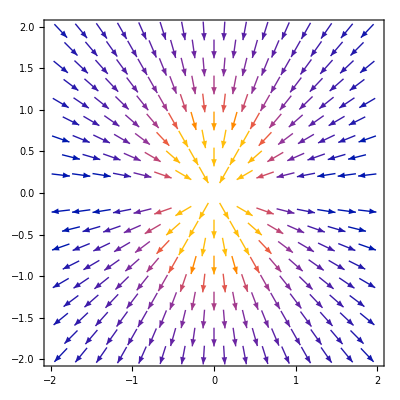

```mathematica
kx=0;
VectorPlot[{-(2 ky kz)/((kx^2+ky^2+kz^2)^2),-(2 kz^2)/((kx^2+ky^2+kz^2)^2)},{ky,-2,2},{kz,-2,2},ScalingFunctions->None]
Clear[kx];
```